```mathematica
RowDelete[x_,entries_]:=Module[{list,i},
list=Table[{entries[[i]]},{i,1,Length[entries]}];
Delete[x,list]
]
(*ColumnDelete takes a matrix and delete the specified columns*)
ColumnDelete[x_,entries_]:=Module[{},
Transpose[RowDelete[Transpose[x],entries]]
]
(*AddZeroToRow adds a zero to a row vector*)
AddZeroToRow[x_,j_]:=Module[{l},
l=Length[x];
Join[Take[x,j-1],{0},Take[x,-(l-j+1)]]
]
(*AddZerosToRow will add any number of zeros to a row vector*)
AddZerosToRow[x_,entries_]:=Module[{y,list,i},
y=x;
list=Sort[entries];
For[i=1,i≤Length[list],i++,
y=AddZeroToRow[y,list[[i]]]
];
y
]


MAR[datasets_, cov_, constraints_]:=Module[{X,U,Y,Z,D,d0,p,x0,u0,y0,one,popdata,covdata,tanks,tankrow,index,tempdata,c,j,k},
p=Length[datasets[[1,1]]]-cov;

If[cov==0,
X={};Y={};
For[j=1,j≤Length[datasets],j++,
x0=Delete[datasets[[j]],Length[datasets[[j]]]];
y0=Delete[datasets[[j]],1];
X=Join[X,x0];
Y=Join[Y,y0]
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1].Inverse[Transpose[ColumnDelete[Z,c+1]].ColumnDelete[Z,c+1]]],c+1]};
D=Join[D,d0]
];
D,

X={};Y={};U={};
For[j=1,j≤Length[datasets],j++,
tempdata=datasets[[j]];
x0=tempdata[[All,cov+1;;cov+p]];
x0=Delete[x0,Length[x0]];
u0=tempdata[[All,1;;cov]];
u0=Delete[u0,Length[u0]];
y0=tempdata[[All,cov+1;;cov+p]];
y0=Delete[y0,1];

X=Join[X,x0];
U=Join[U,u0];
Y=Join[Y,y0];
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[U],Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1+cov].Inverse[Transpose[ColumnDelete[Z,c+1+cov]].ColumnDelete[Z,c+1+cov]]],c+1+cov]};
D=Join[D,d0]
];
D
]
]


ProcessData[raw_,cov_]:=Module[{rawdata,p,tankrow,tanks,purepopdata,logpopdata,covdata,processeddata,index,compdataset,i,i0,j,data},
rawdata=Delete[raw,1];
p=Length[rawdata[[1]]]-cov-1;

tankrow=Delete[raw[[All,1]],1];(*extracts the column of tank labels as a row vector.*)
tanks=DeleteDuplicates[tankrow];(*Just getting a list of tank labels*)

purepopdata=ColumnDelete[rawdata,{1}];
For[i=1,i≤cov,i++,
purepopdata=ColumnDelete[purepopdata,{1}]
];
logpopdata=Log[purepopdata];

If[cov==0,covdata={},
covdata=ColumnDelete[rawdata,{1}];
For[i=1,i≤p,i++,
covdata=ColumnDelete[covdata,{Length[covdata[[1]]]}]
]
];

processeddata=If[cov==0,Transpose[Join[{tankrow},Transpose[logpopdata]]],Transpose[Join[{tankrow},Transpose[covdata],Transpose[logpopdata]]]];(*Join log transformed values back up with tank labels*)

(*Below we extract tank specific processed data and label it by the tank label.*)
For[j=1,j≤Length[tanks],j++,
index=tanks[[j]];
data[index]={};
For[i=1,i≤Length[processeddata],i++,
i0=If[processeddata[[i,1]]==index,{processeddata[[i]]},{}];
data[index]=Join[data[index],i0]
];
data[index]=ColumnDelete[data[index],{1}]
];

compdataset={};
For[j=1,j≤Length[tanks],j++,
index=tanks[[j]];
compdataset=Join[compdataset,{data[index]}]
];
compdataset
]
```

```mathematica
SetDirectory["/Users/4/Documents/Weak interactions/tank data"];
rawdata[1]=Import["CER0.csv"];
rawdata[2]=Import["CER_DAP0.csv"];
rawdata[3]=Import["CER_SCA0.csv"];
rawdata[4]=Import["DAP0.csv"];
rawdata[5]=Import["DAPSCA0.csv"];
rawdata[6]=Import["SCA0.csv"];
rawdata[7]=Import["N0.csv"];
rawdata[8]=Import["N_CER0.csv"];
rawdata[9]=Import["N_CER_DAP0.csv"];
rawdata[10]=Import["N_CER_SCA0.csv"];
rawdata[11]=Import["N_DAP0.csv"];
rawdata[12]=Import["N_SCA0.csv"];
rawdata[13]=Import["N_SCA_DAP0.csv"];
rawdata[14]=Import["N_I_DAP0.csv"];
rawdata[15]=Import["N_I0.csv"];
rawdata[16]=Import["N_I_COP0.csv"];
rawdata[17]=Import["CER_SCA_DAP0.csv"];

(*1 covariate*)
rawdata[18]=Import["CER.csv"];
rawdata[19]=Import["CER_DAP.csv"];
rawdata[20]=Import["CER_SCA.csv"];
rawdata[21]=Import["DAP.csv"];
rawdata[22]=Import["DAPSCA.csv"];
rawdata[23]=Import["SCA.csv"];
rawdata[24]=Import["N.csv"];
rawdata[25]=Import["N_CER.csv"];
rawdata[26]=Import["N_CER_DAP.csv"];
rawdata[27]=Import["N_CER_SCA.csv"];
rawdata[28]=Import["N_Dap.csv"];
rawdata[29]=Import["N_Sca.csv"];
rawdata[30]=Import["N_SCA_DAP.csv"];
rawdata[31]=Import["N_I_DAP.csv"];

(*2 covariates*)
rawdata[32]=Import["N_I.csv"];
rawdata[33]=Import["N_I_cop.csv"];

For[i=1,i≤17,i++,
prodata[i]=ProcessData[rawdata[i],0];
m[i]=MAR[prodata[i],0,{}]
]
For[i=18,i≤33,i++,
prodata[i] = ProcessData[rawdata[i],1];
m[i]=MAR[prodata[i],1,{}]
]

MM={};
For[i=1,i≤17,i++,
tanks=Length[prodata[i]];
MM=Join[MM,{Table[MAR[{prodata[i][[j]]},0,{}],{j,1,tanks}]}]
]
```

```mathematica
(*Find distribution of B matrices (for off-diagonal and on-diagonal) and produce some new B matrices to use as "known" B matrices*)
(*Find covariance matrix of Sigma for the data and use that to produce noise*)
(*Refer to picture on your phone*)
(*Actual data took 26 samples from 6 tanks*)
(*Standard deviation for estimated B matrix should be smaller than known B matrix and tests for stability should be the similar if good estimate*)
```

```mathematica
B[D_]:=Module[{p,cov,B},(*extract B matrix*)
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]]
]
```

```mathematica
For[i=1,i≤33,i++,
p=Length[m[i]];
cov=Length[m[i][[1]]]-p-1;
Amatrix[i] = m[i][[All,1;;1]];
Bmatrix[i] = B[m[i]];
If[cov == 0,
Cmatrix[i] = 0,
Cmatrix[i] = m[i][[All,2;;2+cov-1]]]
]
```

```mathematica
maxt = 50;
X[0] = {0,1,2};
For[t=1,t≤maxt,t++,
X[t] = Amatrix[1] + Bmatrix[1].X[t-1];
]
X[1]
```

{{1.76256},{1.39364},{-0.323391}}

```mathematica
nstr = 0.000001;
For[i=1,i≤17,i++,
Sigma[i]=IdentityMatrix[Length[prodata[i][[1]]]];
For[j=1,j≤Length[prodata[i][[1]]],j++,
For[k=1,k≤j,k++,
Sigma[i][[j,k]]=RandomReal[{-1,1}];
Sigma[i][[k,j]]=Sigma[i][[k,j]]
];
E[i]=RandomReal[{-nstr,nstr},{Length[prodata[i][[1]]]}];
Xlist[i] = {};
For[j=1,j≤ Length[prodata[i]],j++,
prep2 = {};
X[0] = prodata[i][[j,1]];
maxt = 1000;
For[k=1,k≤maxt,k++,
X[k] = Amatrix[i] + Bmatrix[i].X[k-1]+RandomReal[{-nstr,nstr},{Length[X[k-1]],1}];(*this is using the identity matrix as the covariance matrix Sigma; try something else*)
prep1 = {};
For[l=1,l≤Length[X[k]],l++,
prep1 = Join[prep1,X[k][[l]]];
];
prep2 = Join[prep2,{prep1}];
];
Xlist[i] = Join[Xlist[i],{prep2}];
];
Bmatrix2[i]=B[MAR[Xlist[i],0,{}]]
]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{999.,-20374.9,-18955.8,33466.6,14282.3,60273.1},{-20374.9,450354.,429446.,-749700.,-316130.,-1.34624×10^6},{-18955.8,429446.,412419.,-717680.,-301575.,-1.28765×10^6},{33466.6,-749700.,-717680.,1.25071×10^6,526368.,2.24485×10^6},{14282.3,-316130.,-301575.,526368.,221917.,945156.},{60273.1,-1.34624×10^6,-1.28765×10^6,2.24485×10^6,945156.,4.02961×10^6}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

3

```mathematica
Sigma=IdentityMatrix[Length[prodata[1][[1]]]];
For[j=1,j≤20,j++,
For[i=1,i≤Length[Sigma],i++,
Sigma[[i]]=Sigma[[i]]+RandomReal[{-1,1}]*Sigma[[RandomInteger[{1,Length[Sigma]}]]]
]
]
For[j=1,j≤Length[prodata[1][[1]]],j++,
For[k=1,k≤j,k++,
Sigma[[k,j]]=Sigma[[j,k]]
]
]
Sigma
q=RandomReal[{-nstr,nstr},{Length[prodata[1][[1]]]}]*CholeskyDecomposition[Sigma];
```

{{1.63205,0.484354,0.955476,0.776726,-0.822917,7.29364,-0.684798,9.71467,5.91827,3.54013,-2.74504,-0.00105339,8.58578,-5.59733,5.51118,0.592517,10.6763,3.79606,8.75789,3.60969,1.23453,-2.78218,15.1599,-2.55187,-13.1197,4.70358},{0.484354,3.86533,-2.17031,0.215842,0.304508,-2.66563,1.723,-3.50302,-4.29406,4.66924,2.5634,-0.0138706,-7.24861,3.54315,-2.58972,-1.72944,-6.33494,-2.7737,-6.01333,0.378837,-0.160371,0.51752,-9.71503,2.54805,2.49258,-2.73239},{0.955476,-2.17031,1.61231,0.906463,0.409913,-3.5848,0.828706,-2.84076,-0.0154767,-2.93961,1.10003,-0.00632715,-1.56062,1.5643,-0.688292,-0.240383,-0.477835,-1.62788,-3.70851,-3.86172,-0.213504,0.167592,-3.26815,-4.56362,5.98393,-3.24085},{0.776726,0.215842,0.906463,3.63619,0.160927,-0.238397,-1.05181,3.51456,-1.2217,5.77788,-0.903262,-0.0128112,-1.57223,-4.61924,2.19026,0.416164,1.87176,2.37362,-5.96723,5.33011,1.22876,2.57011,2.10433,-0.251815,-1.96234,-2.58184},{-0.822917,0.304508,0.409913,0.160927,0.733879,-0.506443,0.312654,-0.849698,-2.59946,-0.455663,-0.148985,0.0202231,-2.35211,2.28939,-2.25525,0.0334693,-3.12935,-0.221548,-1.96687,0.905369,-1.34807,1.61736,-3.93407,1.36089,1.87555,-1.17046},{7.29364,-2.66563,-3.5848,-0.238397,-0.506443,0.976904,-0.0724116,0.481977,1.14205,-1.34919,-1.28255,0.0202661,1.31112,-0.483893,1.52294,0.264942,1.04141,0.170591,0.846994,-1.0207,0.555681,-0.787096,2.49507,-0.954662,-0.5051,0.998555},{-0.684798,1.723,0.828706,-1.05181,0.312654,-0.0724116,1.56949,-0.505678,3.83074,-1.98206,0.312614,0.00147421,2.25685,-2.20502,2.35945,0.0685451,5.42269,-2.34117,1.80595,-2.93455,0.283405,-1.44382,2.71681,-4.91269,0.148484,-2.25912},{9.71467,-3.50302,-2.84076,3.51456,-0.849698,0.481977,-0.505678,-0.36226,1.78455,0.53345,-1.54383,0.0305672,3.12509,-4.385,1.40021,0.827811,1.15181,1.80374,3.61918,0.510317,-0.0323225,-2.7266,4.4932,3.0347,-1.98807,5.82742},{5.91827,-4.29406,-0.0154767,-1.2217,-2.59946,1.14205,3.83074,1.78455,-4.93867,4.10629,2.07271,0.0213343,-1.45585,-0.121034,-2.64518,0.0751234,-3.73508,3.01664,0.802341,4.95986,-1.36839,2.87285,-2.94016,6.38211,1.00256,2.12391},{3.54013,4.66924,-2.93961,5.77788,-0.455663,-1.34919,-1.98206,0.53345,4.10629,-4.47419,1.13598,0.0293705,5.03556,-5.90663,4.4512,1.65734,3.0718,3.93372,5.74185,-2.97623,0.876171,-2.59004,6.28291,3.09646,3.07044,4.94484},{-2.74504,2.5634,1.10003,-0.903262,-0.148985,-1.28255,0.312614,-1.54383,2.07271,1.13598,-1.73119,-0.0577246,2.62368,-4.80991,5.38676,0.131739,9.36438,-0.515878,-1.24151,-3.1383,1.28079,-2.52947,6.84563,-9.85948,-3.50261,-3.33788},{-0.00105339,-0.0138706,-0.00632715,-0.0128112,0.0202231,0.0202661,0.00147421,0.0305672,0.0213343,0.0293705,-0.0577246,0.0123344,-6.93063,8.78893,-4.13164,-2.25984,-7.75319,-5.0756,-2.11915,-8.18986,-1.30861,-1.18701,-13.9333,-0.781424,10.481,-2.65924},{8.58578,-7.24861,-1.56062,-1.57223,-2.35211,1.31112,2.25685,3.12509,-1.45585,5.03556,2.62368,-6.93063,1.45355,3.33219,1.18442,-0.667326,0.0226271,-2.54678,3.28093,-4.38167,1.74173,-3.92515,1.2156,-0.798287,-2.89092,1.93876},{-5.59733,3.54315,1.5643,-4.61924,2.28939,-0.483893,-2.20502,-4.385,-0.121034,-5.90663,-4.80991,8.78893,3.33219,1.15477,-2.77904,0.27391,-8.06092,4.08587,-0.0925555,2.32359,-0.91981,-0.0917936,-3.04876,8.59374,1.01903,6.95466},{5.51118,-2.58972,-0.688292,2.19026,-2.25525,1.52294,2.35945,1.40021,-2.64518,4.4512,5.38676,-4.13164,1.18442,-2.77904,-8.31469,-1.29942,-13.3282,-3.71506,-7.05944,0.565991,-1.54306,6.03062,-16.4062,4.59333,10.0276,-5.18169},{0.592517,-1.72944,-0.240383,0.416164,0.0334693,0.264942,0.0685451,0.827811,0.0751234,1.65734,0.131739,-2.25984,-0.667326,0.27391,-1.29942,0.435276,6.96218,1.51599,0.619403,-1.59198,1.46331,-2.7431,6.07347,-4.56647,-3.53944,-0.187706},{10.6763,-6.33494,-0.477835,1.87176,-3.12935,1.04141,5.42269,1.15181,-3.73508,3.0718,9.36438,-7.75319,0.0226271,-8.06092,-13.3282,6.96218,6.5526,4.41253,-3.33384,4.08975,-0.0724279,0.707861,7.8902,-2.78273,-2.48483,-0.578524},{3.79606,-2.7737,-1.62788,2.37362,-0.221548,0.170591,-2.34117,1.80374,3.01664,3.93372,-0.515878,-5.0756,-2.54678,4.08587,-3.71506,1.51599,4.41253,2.99489,13.4051,-1.30307,2.15643,-8.69186,30.9106,-14.0776,-18.7694,4.46155},{8.75789,-6.01333,-3.70851,-5.96723,-1.96687,0.846994,1.80595,3.61918,0.802341,5.74185,-1.24151,-2.11915,3.28093,-0.0925555,-7.05944,0.619403,-3.33384,13.4051,0.564379,2.25779,-0.75963,3.0814,-2.04399,1.87222,1.57433,-0.307314},{3.60969,0.378837,-3.86172,5.33011,0.905369,-1.0207,-2.93455,0.510317,4.95986,-2.97623,-3.1383,-8.18986,-4.38167,2.32359,0.565991,-1.59198,4.08975,-1.30307,2.25779,-1.36294,1.08699,-1.91224,7.01126,-4.81368,-3.97546,0.727519},{1.23453,-0.160371,-0.213504,1.22876,-1.34807,0.555681,0.283405,-0.0323225,-1.36839,0.876171,1.28079,-1.30861,1.74173,-0.91981,-1.54306,1.46331,-0.0724279,2.15643,-0.75963,1.08699,2.22846,-4.83744,9.97845,1.00521,-7.45845,5.88934},{-2.78218,0.51752,0.167592,2.57011,1.61736,-0.787096,-1.44382,-2.7266,2.87285,-2.59004,-2.52947,-1.18701,-3.92515,-0.0917936,6.03062,-2.7431,0.707861,-8.69186,3.0814,-1.91224,-4.83744,-5.25124,8.7696,-1.51291,-13.6266,3.69009},{15.1599,-9.71503,-3.26815,2.10433,-3.93407,2.49507,2.71681,4.4932,-2.94016,6.28291,6.84563,-13.9333,1.2156,-3.04876,-16.4062,6.07347,7.8902,30.9106,-2.04399,7.01126,9.97845,8.7696,3.64577,-2.10772,-5.79204,0.58061},{-2.55187,2.54805,-4.56362,-0.251815,1.36089,-0.954662,-4.91269,3.0347,6.38211,3.09646,-9.85948,-0.781424,-0.798287,8.59374,4.59333,-4.56647,-2.78273,-14.0776,1.87222,-4.81368,1.00521,-1.51291,-2.10772,0.546462,-2.99948,6.06751},{-13.1197,2.49258,5.98393,-1.96234,1.87555,-0.5051,0.148484,-1.98807,1.00256,3.07044,-3.50261,10.481,-2.89092,1.01903,10.0276,-3.53944,-2.48483,-18.7694,1.57433,-3.97546,-7.45845,-13.6266,-5.79204,-2.99948,2.97906,-2.52607},{4.70358,-2.73239,-3.24085,-2.58184,-1.17046,0.998555,-2.25912,5.82742,2.12391,4.94484,-3.33788,-2.65924,1.93876,6.95466,-5.18169,-0.187706,-0.578524,4.46155,-0.307314,0.727519,5.88934,3.69009,0.58061,6.06751,-2.52607,2.63975}}

CholeskyDecomposition::posdef: The matrix {{1.63205,0.484354,0.955476,0.776726,-0.822917,7.29364,-0.684798,9.71467,5.91827,3.54013,-2.74504,-0.00105339,8.58578,-5.59733,5.51118,0.592517,10.6763,3.79606,8.75789,3.60969,1.23453,-2.78218,15.1599,-2.55187,-13.1197,4.70358},«24»,{4.70358,-2.73239,-3.24085,-2.58184,-1.17046,0.998555,-2.25912,5.82742,2.12391,4.94484,-3.33788,«5»,-0.578524,4.46155,-0.307314,0.727519,5.88934,3.69009,0.58061,6.06751,-2.52607,2.63975}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

```mathematica
For[i=1,i≤17,i++,
Bnorm1[i] = Norm[Bmatrix[i],"Frobenius"];
B2norm1[i] = Norm[Bmatrix2[i],"Frobenius"];
dif[i]=Norm[(Bmatrix[i]-Bmatrix2[i])/(Bmatrix[i]*2*nstr),"Frobenius"] (*Find error relative to strength of noise*)
]
?dif
```

Global`dif

dif[1]=2.08785
 
dif[2]=42.943
 
dif[3]=23.0345
 
dif[4]=1.43397
 
dif[5]=11.5231
 
dif[6]=10.7907
 
dif[7]=34.0127
 
dif[8]=70.5291
 
dif[9]=33.4389
 
dif[10]=364.355
 
dif[11]=13.08
 
dif[12]=3137.23
 
dif[13]=154.46
 
dif[14]=115.264
 
dif[15]=33.166
 
dif[16]=61.5768
 
dif[17]=597.793

```mathematica
count = 0;
Xlist1 = {};
prep1={};
prep2={};
For[i=1,i≤1000,i++,
count = 0;
For[t=-5,t≤1,t+=0.1,
count = count + 1;
strength[count] = 10^t;
Xlist1 = {};
For[j=1,j≤ Length[prodata[1]],j++,
prep2 = {};
X[0] = prodata[1][[j,1]];
maxt = 1000;
For[k=1,k≤maxt,k++,
X[k] = Amatrix[1] + Bmatrix[1].X[k-1]+RandomReal[{-strength[count],strength[count]},{Length[X[k-1]],1}];(*this is using the identity matrix as the covariance matrix Sigma; try something else*)
prep1 = {};
For[l=1,l≤Length[X[k]],l++,
prep1 = Join[prep1,X[k][[l]]]
];
prep2 = Join[prep2,{prep1}]
];
Xlist1 = Join[Xlist1,{prep2}]
];
Bmatrix3=B[MAR[Xlist1,0,{}]];
relerr[count] = Abs[(Bmatrix[1]-Bmatrix3)/Bmatrix[1]];
relerrn[count] = Norm[relerr[count],"Frobenius"];
relerrs[count] = Norm[relerr[count] / ( strength[count]),"Frobenius"]
];
If[i==1,
For[j=1,j≤count,j++,
relerrtot[j] = relerr[j];
relerrntot[j] =  relerrn[j];
relerrstot[j] = relerrs[j];
],
For[j=1,j≤count,j++,
relerrtot[j] = relerrtot[j] + relerr[j];
relerrntot[j] = relerrntot[j] + relerrn[j];
relerrstot[j] = relerrntot[j] + relerrs[j];
relerravg[j] = relerrtot[j] / i;
relerrnavg[j] = relerrntot[j] / i;
relerrsavg[j] = relerrstot[j] / i
]
]
]
```

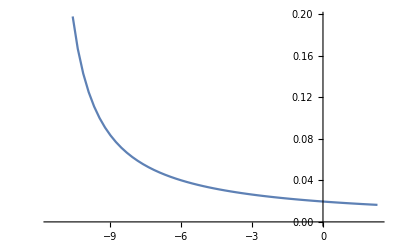

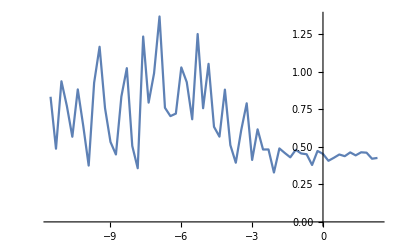

```mathematica
f[x_]:=1/x
ListLinePlot[Table[{Log[strength[x]],f[x]},{x,1,count}]]
ListLinePlot[Table[{Log[strength[x]],relerrsavg[x]},{x,1,count}]]
```

```mathematica
relerr[70]/strength[70]
```

{{0.000263977,0.000109265,0.00161531},{0.00499185,0.0000876318,0.000561375},{0.00216593,0.0000826413,0.00120249}}

```mathematica
Length[prodata[1]]
```

6